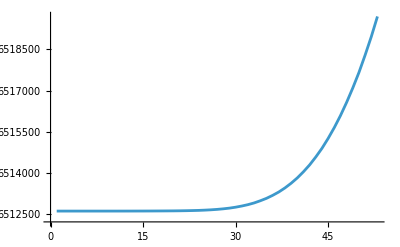

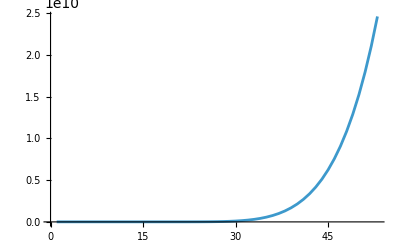

```mathematica
SetDirectory[NotebookDirectory[]];
Re1=Flatten[Import["Re.dat"]];
Im1=Flatten[Import["Im.dat"]];
omega=Flatten[Import["omega.dat"]];
mr2=Flatten[Import["mrho2bare.dat"]];
mrphy=Flatten[Import["m_rho_phy.dat"]];
Zphi=Flatten[Import["Zphi.dat"]];
repart=Transpose[{omega,Re1}];
Impart=Transpose[{omega,Im1}];
ListLinePlot[√mr2,PlotRange->All]
ListLinePlot[Re1,PlotRange->All]
```

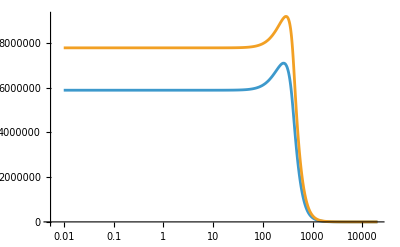

```mathematica
k=Flatten[Import["./kMeV.dat"]];
re=Flatten[Import["./gammarho_Re.dat"]];
Zpi=Flatten[Import["./Zphi_p0.dat"]];
Redata=Transpose[{k,re}];
Zdata=Transpose[{k,Zpi}];
ListLinePlot[{Redata,Zdata},PlotRange->All,ScalingFunctions->{"Log",Automatic}]
```